```mathematica
a=0.2;
b=0.4;
c=0.3;
X[x]:=Piecewise[{{0,x<=a},{0,x>=1-b}},c Sin[(2 π)/(1-a-b)( x-a)]];
Plot[X[x],{x,0,1},AxesOrigin->{0,0},PlotRange->{{0,1},{-1,1}}]
```

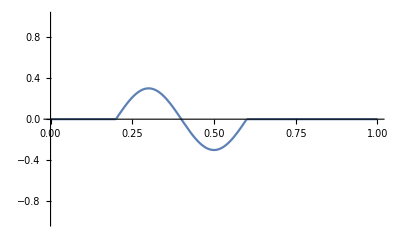

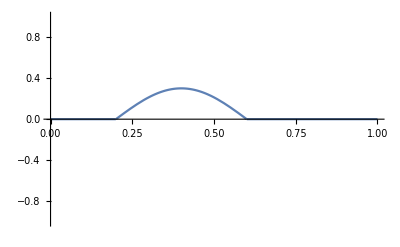

```mathematica
a=0.2;
b=0.4;
c=0.3;
Z[x]:=Piecewise[{{0,x<=a},{0,x>=1-b}},c Sin[π/(1-a-b)( x-a)]];
Plot[Z[x],{x,0,1},AxesOrigin->{0,0},PlotRange->{{0,1},{-1,1}}]
```